```mathematica
pts={{{0},0,1},{{1},1,0},{{1.25},.8,0},{{1.6},1.25,0},{{1.8},1.25,0},{{2.25},.5,0},{{3},2,0},{{3.5},1,0},{{3.65},1,0},{{4},0,-1}};
```

```mathematica
intp = Interpolation[pts]
```

InterpolatingFunction[…]

```mathematica
lokEpilog={Gray,Dashed,Line[{{3,0},{3,2}}],Line[{{1,0},{1,1}}],Red, PointSize[Large],Point[{3,0}],Point[{1,0}]};
```

```mathematica
globEpilog={Gray,Dashed,Line[{{3,0},{3,2}}],Red, PointSize[Large],Point[{3,0}]};
```

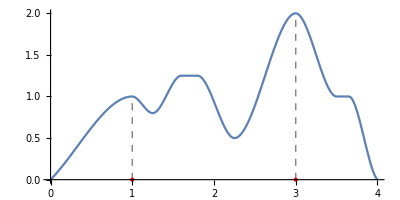

```mathematica
Plot[intp[x],{x,0,4},AspectRatio->Automatic,Epilog->lokEpilog]
```

```mathematica
intp2= Interpolation[{#[[1]][[1]],#[[2]]}&/@pts,InterpolationOrder->1]
```

InterpolatingFunction[…]

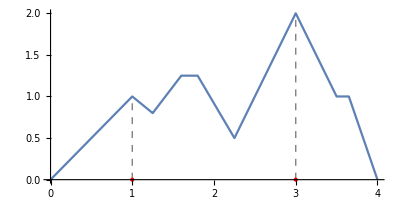

```mathematica
Plot[intp2[x],{x,0,4},AspectRatio->Automatic,Epilog->lokEpilog]
```

```mathematica
ptsAlt={{{0},0,2},{{.25},1.2,0},{{.5},1,0},{{1},2,0},{{1.5},.7,0},{{2},2,0},{{2.5},2,0},{{3},1.3,0},{{3.5},2,0},{{4},0,-2}};
```

```mathematica
intp3=Interpolation[ptsAlt]
```

InterpolatingFunction[…]

```mathematica
altGlobEpilog={Gray,Dashed,Line[{{0,2},{3.5,2},{3.5,0}}],Line[{{1,0},{1,2}}],Line[{{2,0},{2,2}}],Line[{{2.5,0},{2.5,2}}],Red,PointSize[Large],Point[{1,0}],Point[{3.5,0}],Point[{2,0}],Point[{2.5,0}],Thick,Dashing[{}],Line[{{2,0},{2.5,0}}]};
```

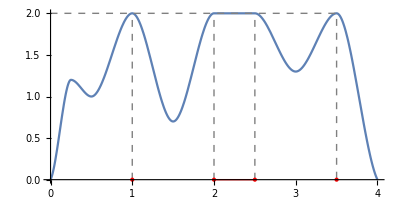

```mathematica
Plot[intp3[x],{x,0,4},AspectRatio->Automatic,Epilog->altGlobEpilog]
```

```mathematica
intp4= Interpolation[{#[[1]][[1]],#[[2]]}&/@ptsAlt,InterpolationOrder->1]
```

InterpolatingFunction[…]

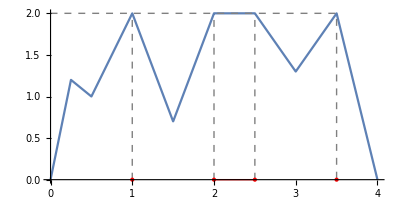

```mathematica
Plot[intp4[x],{x,0,4},AspectRatio->Automatic,Epilog->altGlobEpilog]
```

```mathematica
ptsX={{{0},0,1},{{1},1,0},{{1.25},.8,0},{{1.6},1.25,0},{{1.8},1.25,0},{{2.25},.5,0},{{2.5},.5,0},{{3},2,0},{{3.5},1,0},{{3.65},1,0},{{4},0,-1}};
```

```mathematica
intp5=Interpolation[ptsX]
```

InterpolatingFunction[…]

```mathematica
lokEpilogX={Gray,Dashed,Line[{{3,0},{3,2}}],Line[{{1,0},{1,1}}],Line[{{1.6,0},{1.6,1.25}}],Line[{{1.8,0},{1.8,1.25}}],Line[{{2.25,0},{2.25,.5}}], Line[{{2.5,0},{2.5,.5}}],Line[{{3.5,0},{3.5,1}}],Line[{{3.65,0},{3.65,1}}],Red,Dashing[{}], PointSize[Large],Point[{3,0}],Point[{1,0}],Thick,Line[{{1.6,0},{1.8,0}}],Line[{{3.5,0},{3.65,0}}],Line[{{2.25,0},{2.5,0}}],Point[{1.6,0}],Point[{1.8,0}],Point[{3.65,0}],White,EdgeForm[{Red,Thick}],Disk[{2.5,0},.04],Disk[{2.25,0},.04],Disk[{3.5,0},.04]};
```

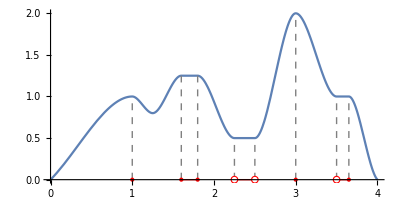

```mathematica
Plot[intp5[x],{x,0,4},AspectRatio->Automatic,Epilog->lokEpilogX]
```

```mathematica
intp6= Interpolation[{#[[1]][[1]],#[[2]]}&/@ptsX,InterpolationOrder->1]
```

InterpolatingFunction[…]

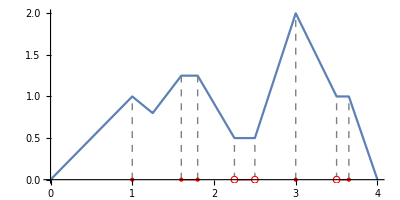

```mathematica
Plot[intp6[x],{x,0,4},AspectRatio->Automatic,Epilog->lokEpilogX]
```

```mathematica
warnEpilog={Gray,Dashed,Line[{{0,2},{3.5,2},{3.5,0}}],Line[{{1,0},{1,2}}],Red,PointSize[Large],Point[{1,0}],Point[{3.5,0}]};
```

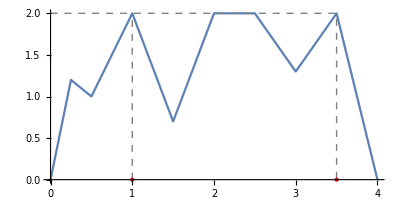

```mathematica
Plot[intp4[x],{x,0,4},AspectRatio->Automatic,Epilog->warnEpilog]
```